### Definition

```mathematica
δa[r_]=(E^(-r^2/(2 a^2)))/((2π)^(3/2)a^3);α=Rationalize@0.4;u0=10^-20;δstart=10^-10;m=1;αSch=2m;ee={10^-10,10^-5,0.001,0.003,0.007,0.01,0.03,0.07,0.1,0.3,0.7,1};
Vs1[r_,a_,c1_]=- α/r Erf[r/(√2 a)]+c1 a^2 δa[r];
Vs2[r_,a_,{c2_,d1_}]=N[- 1/# Erf[#/(√2 a)]+c2 a^2 δa[#]+d1 a^4 Laplacian[Rationalize@δa[#],{#,θ,ϕ},"Spherical"]&[r]];V[r_]=-α/r;
```

```mathematica
RS[n_,r_]=2/(A^(3/2) n^(3/2)) ⅇ^(-r/(n A)) Hypergeometric1F1[1-n,2,(2 r)/(n A)]/.A->Rationalize@(1/(m α));
```

```mathematica
RealEigenEnergy[n_]=-(m α^2)/(2 n^2);
Table20REE=Table[RealEigenEnergy[n],{n,20}]
```

{-2/25,-1/50,-2/225,-1/200,-2/625,-1/450,-2/1225,-1/800,-2/2025,-1/1250,-2/3025,-1/1800,-2/4225,-1/2450,-2/5625,-1/3200,-2/7225,-1/4050,-2/9025,-1/5000}

```mathematica
Needs["NumericalCalculus`"]
```

```mathematica
EigenEnergy[V_,αSch_,{min_,max_},{opt1___},{opt2___}]:=
Module[{sol,ef,evShifted,evnew,steps=∞,time1,time2},
PrintTemporary[V];
(*Module[{shift=10,d=1000,n=20,ev},{ev,ef}=NDEigensystem[{shift f[r]+V f[r]-1/αSch f''[r](*+NeumannValue[0,r==d]*),DirichletCondition[f[r]==0,True]},f[r],{r,0,d},n,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.05}}},"Eigensystem"->{"Arnoldi",MaxIterations->Infinity}}];
evShifted=ev-shift];
Print[evShifted];*)
sol=ParametricNDSolve[{V u[r]-1/αSch u''[r]==e u[r],u'[max]==-min,u[max]==min},u,{r,min,max},e,MaxSteps->steps,opt1];
evnew=e/.#&/@
Table[
PrintTemporary[n];FindRoot[u[e][min]==0/.sol,{e,0.99 SetPrecision[#[[n]],3],1.01 SetPrecision[#[[n]],3]}&[Table20REE],opt2(*,StepMonitor:>PrintTemporary[e]*)],{n,20}]
]
δ50e[en_,V_]:=Module[{sol,δs,δr,r1=50,r2=u0,β,jder,nder,k,wpc=50,prc=20,time1,time2},
time1=SessionTime[];
k=√(2en);
β:=r1 u'[r1]/u[r1]-1;
jder[r_]=D[SphericalBesselJ[0,r],r];
nder[r_]=D[SphericalBesselY[0,r],r];sol=Flatten@NDSolve[{u''[r]+αSch(en-V)u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},PrecisionGoal->prc,WorkingPrecision->wpc, MaxSteps->Infinity,InterpolationOrder->All(*,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}*)(*,SolveDelayed->True*)];
δs=FindRoot[(*u'[r1]/u[r1]==k Cot[k r1+δ]*)Tan[δ]==(k r1 jder[k r1]-β SphericalBesselJ[0,k r1])/(k r1 nder[k r1]-β SphericalBesselY[0,k r1])(*u'[r1]/u[r1]==(k+1/(k r1)) Cot[k r1+δ+Log[2 k r1]/k]*)/.sol,{δ,0},WorkingPrecision->wpc,PrecisionGoal->prc];
δr=δ/.δs;
time2=SessionTime[];
(*PrintTemporary["End with "<>ToString[time2-time1]<>"s"];*)
δr=NestWhile[Sign[#](Abs[#]-π)&,δr,Abs[#]>π/2&]
]
δ50[V_]:=Module[{en,len,δen,timestampa,timestampb},
len=Length@ee;
ParallelTable[
timestampa=SessionTime[];
en=ee[[i]];
δen=δ50e[en,V];
timestampb=SessionTime[];
PrintTemporary[{en,δen},"    ",timestampb-timestampa];
δen,{i,2,len}]
]
Eigenfun[V_,enelist_]:=Module[{},Flatten[With[{r1=2000,r2=1.*10^-50},NDSolve[{V f[r]-1/αSch f''[r]==# f[r],f[r1]==r2,f'[r1]==-r2},f,{r,r1,r2},WorkingPrecision->50,AccuracyGoal->30,PrecisionGoal->15,InterpolationOrder->All,MaxSteps->Infinity,MaxStepSize->0.01,Method->{"Shooting","StartingInitialConditions"->{f'[r2]==1,f[r2]==r2}}]]&/@enelist,2]]
```

```mathematica
Eigenfunsin[V_,ene_,rr_,{r1_,r2_},opt___]:=
Module[{efunction,amplitude},efunction=Flatten[NDSolve[{V f[r]-1/αSch f''[r]==ene f[r],f[r1]==r2,f'[r1]==-r2},f,{r,r1,r2},opt,Method->{"Shooting","StartingInitialConditions"->{f'[r2]==1,f[r2]==r2}}],2];
amplitude=NIntegrate[f[r]^2/.#,{r,r2,r1}]^-0.5&/@efunction;
amplitude f[rr]/.efunction
]
```

```mathematica
EigenEnergySolo[V_,αSch_,{min_,max_},{estart_,eend___},{opt1___},{opt2___}]:=
Module[{sol,ef,evShifted,evnew,steps=∞,time1,time2},
PrintTemporary[V];
sol=ParametricNDSolve[{V u[r]-1/αSch u''[r]==e u[r],u[max]==min,u'[max]==-min},u,{r,min,max},e,MaxSteps->steps,(*StepMonitor:>PrintTemporary[{r,u[e][r]}],*)opt1];
PrintTemporary[{estart,eend}];
time2=SessionTime[];
evnew=e/.#&/@
FindRoot[u[e][min]==0/.sol,{e,estart,eend},opt2,StepMonitor:>{time1=time2;time2=SessionTime[];Print[{e,u[e][min]/.sol},"time:",time2-time1,"s"]}]]
```

```mathematica
δexpminus10=δ50e[10^-10,V[r]];
δexpminus9=δ50e[10^-9,V[r]];
δexpminus5=δ50e[10^-5,V[r]];
(*δ50V=δ50[V[r]]*)
```

FindRoot::precw: The precision of the argument function (TraditionalForm`tan(δ) == -0.000799356024108875307158800370015696288485754568172) is less than WorkingPrecision (TraditionalForm`50.`).

FindRoot::precw: The precision of the argument function (TraditionalForm`tan(δ) == -0.00252779037141606535634764484961214551074983799219) is less than WorkingPrecision (TraditionalForm`50.`).

FindRoot::precw: The precision of the argument function (TraditionalForm`tan(δ) == -0.258100960992136653725175035849101347847353159394) is less than WorkingPrecision (TraditionalForm`50.`).

### Determine c_1

```mathematica
hhhc1[en_,a_,c1_?NumberQ]:=δ50e[en,Vs1[r,a,c1]];
evnhhhc1[c1_]:=N[hhhc1[10^-10,a,c1]-δexpminus10,8];
Determinec1[a_,{start_,end___},opt___]:=Module[{findroot},
Print[a];
findroot=FindRoot[hhhc1[10^-10,a,c1]==δexpminus10,{c1,start,end},opt];
Print[c1/.findroot];
c1/.findroot
]
```

```mathematica
c1a={};
```

```mathematica
Module[{table},
table=ParallelTable[Block[{c1,a},
a=10^loga;
c1=Determinec1[a,{0},{MaxIterations->If[a>10,200,100],PrecisionGoal->10,WorkingPrecision->50}];
{a,c1}],{loga,DeleteDuplicates[Join[Range[2,1,-0.01],Range[1,0,-0.01],Range[0,-1,-0.1],Range[-1,-3,-0.4],Range[-3,-5,-0.5]]]}];
c1a=DeleteDuplicates@Sort[c1a~Join~table]
]
```

100.

72.4436

52.4807

38.0189

NDSolve::precw: The precision of the differential equation (TraditionalForm`) is less than WorkingPrecision (TraditionalForm`50.`).

FindRoot::precw: The precision of the argument function (TraditionalForm`tan(δ) == -0.000511415484670652805986528469150831600615128099508) is less than WorkingPrecision (TraditionalForm`50.`).

FindRoot::precw: The precision of the argument function (TraditionalForm`tan(δ) == 0.00116480453183571190389347739469494026351577769226) is less than WorkingPrecision (TraditionalForm`50.`).

FindRoot::precw: The precision of the argument function (TraditionalForm`tan(δ) == -0.000881090745088325258622180549762585458755302986047) is less than WorkingPrecision (TraditionalForm`50.`).

FindRoot::precw: The precision of the argument function (TraditionalForm`tan(δ) == -0.0007163673299077932858937084468158033008664936623) is less than WorkingPrecision (TraditionalForm`50.`).

NDSolve::precw: The precision of the differential equation (TraditionalForm`) is less than WorkingPrecision (TraditionalForm`50.`).

FindRoot::precw: The precision of the argument function (TraditionalForm`tan(δ) == -0.000511415484670652805986528469150831600615128099508) is less than WorkingPrecision (TraditionalForm`50.`).

FindRoot::precw: The precision of the argument function (TraditionalForm`tan(δ) == 0.00116480453183571190389347739469494026351577769226) is less than WorkingPrecision (TraditionalForm`50.`).

FindRoot::precw: The precision of the argument function (TraditionalForm`tan(δ) == -0.000881090745088325258622180549762585458755302986047) is less than WorkingPrecision (TraditionalForm`50.`).

FindRoot::precw: The precision of the argument function (TraditionalForm`tan(δ) == -0.0007163673299077932858937084468158033008664936623) is less than WorkingPrecision (TraditionalForm`50.`).

NDSolve::precw: The precision of the differential equation (TraditionalForm`) is less than WorkingPrecision (TraditionalForm`50.`).

General::stop: Further output of NDSolve :: precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (TraditionalForm`tan(δ) == -0.000511415486638207592851515519906446451824500675529) is less than WorkingPrecision (TraditionalForm`50.`).

FindRoot::precw: The precision of the argument function (TraditionalForm`tan(δ) == 0.00116480438771166240849032919388184783201805904068) is less than WorkingPrecision (TraditionalForm`50.`).

FindRoot::precw: The precision of the argument function (TraditionalForm`tan(δ) == -0.000881090747898818012751017579285821687175920200723) is less than WorkingPrecision (TraditionalForm`50.`).

FindRoot::precw: The precision of the argument function (TraditionalForm`tan(δ) == -0.00071636733088234125415093802877606069633027208827) is less than WorkingPrecision (TraditionalForm`50.`).

General::stop: Further output of FindRoot :: precw will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than TraditionalForm`50.` digits of working precision to meet these tolerances.

2.6096504327932562928715239603713952809877735608032

97.7237

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than TraditionalForm`50.` digits of working precision to meet these tolerances.

-0.60679610198406898274197336764294752903028876117741

51.2861

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than TraditionalForm`50.` digits of working precision to meet these tolerances.

3.3801159535282439269368554704658210204721007635661

70.7946

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than TraditionalForm`50.` digits of working precision to meet these tolerances.

0.9825798794468639855592317768477551133186906414305

37.1535

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than TraditionalForm`50.` digits of working precision to meet these tolerances.

3.4306664250792854255496578330480555692541533296937

69.1831

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than TraditionalForm`50.` digits of working precision to meet these tolerances.

-0.48249548251543516446970922599733539553156926020828

50.1187

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than TraditionalForm`50.` digits of working precision to meet these tolerances.

2.6699949471497554827121550677711442964691688356493

95.4993

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than TraditionalForm`50.` digits of working precision to meet these tolerances.

1.0872071305382174217635806221250222904781663162267

36.3078

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than TraditionalForm`50.` digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

-0.36025804273648925760188682137561285855881906433845

48.9779

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than TraditionalForm`50.` digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

2.7293417843049603512509778424181068485466751905869

93.3254

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than TraditionalForm`50.` digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

-2.2962985329290036984512191252170464561757375255314

67.6083

2.787735089828201114734693114979505389084905825753

91.2011

-0.23998242791214254303899637916878881324573450333494

47.863

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than TraditionalForm`50.` digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

1.1911744563101472868767640729102141771833839361178

35.4813

2.8452192125145932142881312393138757502488089840634

89.1251

-0.12156720709309539004615328492421854251787517037205

46.7735

-2.1393021600858984825232742253460359591391275885236

66.0693

2.9018387760816420740003599929683935189987966208832

87.0964

1.2945747767757147081664566053018573279576219805636

34.6737

2.9576387552263807613369633603888308218852605742635

85.1138

-0.0049108667120548961596536511397935385919632770099689

45.7088

-1.9855966977415459676209133910587720619252832809927

64.5654

3.0126645565394652544670722814353178587581938430154

83.1764

1.3974982663839171891095367108283875199163523916561

33.8844

0.1100881777722080196815526240718385383848621211974

44.6684

3.0669621048315436679696420592530735442697120522745

81.2831

-1.8350774931016023897865611467623051624601600135779

63.0957

0.22353154913582490061556044261395882049330529315314

43.6516

3.1205779354940261729886999064150352458059144492288

79.4328

1.5000318281754617427077239904234076158213867795321

33.1131

0.33552085117811130332964007326868712110321422981508

42.658

3.1735592935920688406862988757372172586694331363988

77.6247

-1.6876405886826946392093846202930775460642134076029

61.6595

0.44615758335010949214427126085586161625666325506378

41.6869

1.6022585412699899510699352694736320669177398874576

32.3594

3.2259542404736112667734745260294094269248768830591

75.8578

-1.5431826359090348424760890923705242310533366969372

60.256

3.2778117687759315315104567547746788318483173070582

74.131

1.7042571005985301604016530222310459936994122871889

31.6228

0.55554302327569786031078832355459320138977392586393

40.738

3.3291819268223616723955273391769295677600744605973

27.5423

NDSolve::precw: The precision of the differential equation (TraditionalForm`) is less than WorkingPrecision (TraditionalForm`50.`).

FindRoot::precw: The precision of the argument function (TraditionalForm`tan(δ) == -0.000597957360505896831496850321982922585925073975482) is less than WorkingPrecision (TraditionalForm`50.`).

NDSolve::precw: The precision of the differential equation (TraditionalForm`) is less than WorkingPrecision (TraditionalForm`50.`).

FindRoot::precw: The precision of the argument function (TraditionalForm`tan(δ) == -0.000597957360505896831496850321982922585925073975482) is less than WorkingPrecision (TraditionalForm`50.`).

NDSolve::precw: The precision of the differential equation (TraditionalForm`) is less than WorkingPrecision (TraditionalForm`50.`).

General::stop: Further output of NDSolve :: precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (TraditionalForm`tan(δ) == -0.000597957362082309494572060578335115744503284514367) is less than WorkingPrecision (TraditionalForm`50.`).

General::stop: Further output of FindRoot :: precw will be suppressed during this calculation.

-1.4016008102221862558385479486102691616707322395984

58.8844

1.8061012751266137809970105183886715459178789197156

30.903

-1.2627927281670338820287027168633967447986763848658

57.544

0.66377807304498001803138968986121736773569249497267

39.8107

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than TraditionalForm`50.` digits of working precision to meet these tolerances.

2.4173381685459029829497760482476480875730414504815

26.9153

-1.1266563670160201521721589415976950004645140007713

56.2341

1.907859419067021355892456500173173592599180743135

30.1995

0.77096306512643165643765582896515641687227009662048

38.9045

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than TraditionalForm`50.` digits of working precision to meet these tolerances.

2.5196865968703687126175018192708733804867453638127

26.3027

-0.99308998760874389969899952370567886928763202286159

54.9541

2.0095940793168685192722896670339667693014583111771

29.5121

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than TraditionalForm`50.` digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

2.6222691749580214760041979254047588638581462620477

25.704

0.87719752392031545725403820559097807601856776696312

19.9526

NDSolve::precw: The precision of the differential equation (TraditionalForm`) is less than WorkingPrecision (TraditionalForm`50.`).

FindRoot::precw: The precision of the argument function (TraditionalForm`tan(δ) == 0.0026497048299925230239117778821596956635972164239) is less than WorkingPrecision (TraditionalForm`50.`).

NDSolve::precw: The precision of the differential equation (TraditionalForm`) is less than WorkingPrecision (TraditionalForm`50.`).

FindRoot::precw: The precision of the argument function (TraditionalForm`tan(δ) == 0.0026497048299925230239117778821596956635972164239) is less than WorkingPrecision (TraditionalForm`50.`).

NDSolve::precw: The precision of the differential equation (TraditionalForm`) is less than WorkingPrecision (TraditionalForm`50.`).

General::stop: Further output of NDSolve :: precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (TraditionalForm`tan(δ) == 0.0026497041327614115728711394526897014408097493749) is less than WorkingPrecision (TraditionalForm`50.`).

General::stop: Further output of FindRoot :: precw will be suppressed during this calculation.

-0.86199206121714510589141233139880989485340888000839

53.7032

2.1113617508470121172964448938435372024397923580721

28.8403

2.7251168356275948578751577865037448986823959129728

25.1189

-0.73326120139976156597527550695327246078534847007712

14.4544

NDSolve::precw: The precision of the differential equation (TraditionalForm`) is less than WorkingPrecision (TraditionalForm`50.`).

FindRoot::precw: The precision of the argument function (TraditionalForm`tan(δ) == -0.000842544628057185922478288384925027838454026107707) is less than WorkingPrecision (TraditionalForm`50.`).

NDSolve::precw: The precision of the differential equation (TraditionalForm`) is less than WorkingPrecision (TraditionalForm`50.`).

FindRoot::precw: The precision of the argument function (TraditionalForm`tan(δ) == -0.000842544628057185922478288384925027838454026107707) is less than WorkingPrecision (TraditionalForm`50.`).

NDSolve::precw: The precision of the differential equation (TraditionalForm`) is less than WorkingPrecision (TraditionalForm`50.`).

General::stop: Further output of NDSolve :: precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (TraditionalForm`tan(δ) == -0.000842544629790635950582056452710718896514391870512) is less than WorkingPrecision (TraditionalForm`50.`).

General::stop: Further output of FindRoot :: precw will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than TraditionalForm`50.` digits of working precision to meet these tolerances.

3.8903393175639868015249551396463197206134292490311

19.4984

2.8282617783039389854331016628273304135141524373956

24.5471

2.2132128389798866983114101612415065053335316846975

28.1838

2.931740235590105629083595919342544281181394764686

23.9883

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than TraditionalForm`50.` digits of working precision to meet these tolerances.

-0.45974137537277172470837633654608282952047095763114

14.1254

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than TraditionalForm`50.` digits of working precision to meet these tolerances.

-1.9138664790350308703454011058995132458456176584851

19.0546

2.3151918920738303907350166278857544832687722201496

10.4713

NDSolve::precw: The precision of the differential equation (TraditionalForm`) is less than WorkingPrecision (TraditionalForm`50.`).

FindRoot::precw: The precision of the argument function (TraditionalForm`tan(δ) == -0.000735933549349189457863471437453963279315424473784) is less than WorkingPrecision (TraditionalForm`50.`).

NDSolve::precw: The precision of the differential equation (TraditionalForm`) is less than WorkingPrecision (TraditionalForm`50.`).

FindRoot::precw: The precision of the argument function (TraditionalForm`tan(δ) == -0.000735933549349189457863471437453963279315424473784) is less than WorkingPrecision (TraditionalForm`50.`).

NDSolve::precw: The precision of the differential equation (TraditionalForm`) is less than WorkingPrecision (TraditionalForm`50.`).

General::stop: Further output of NDSolve :: precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (TraditionalForm`tan(δ) == -0.000735933549975382570585435039146120036594243437075) is less than WorkingPrecision (TraditionalForm`50.`).

General::stop: Further output of FindRoot :: precw will be suppressed during this calculation.

3.0355956103684798062487586285904890992542624547627

23.4423

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than TraditionalForm`50.` digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

-1.803511844997614830607556957115645156612322673179

18.6209

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than TraditionalForm`50.` digits of working precision to meet these tolerances.

-0.34528606543433985523011199885107658582664322568538

13.8038

3.1398818891106518218598152408258748205169275102824

22.9087

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than TraditionalForm`50.` digits of working precision to meet these tolerances.

1.1711908458506466273188080632523346470051059836454

10.2329

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than TraditionalForm`50.` digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

-0.23044656620857820485798466358019351707560027369791

13.4896

-1.6931209537092735416781468142601610671137786143245

18.197

3.2446672150522421907632960399090233543674399729883

22.3872

3.3500374951825001843798800417099604748701915823852

21.8776

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than TraditionalForm`50.` digits of working precision to meet these tolerances.

1.2891969410417437335664723804968436995441273204968

10.

-1.5826057987541382876042692061969105036080646879337

17.7828

-0.11523572386224370373823456143798709749788726150492

13.1826

3.4560999203867467552942446617330244147415742116767

21.3796

-1.4718908866790919193307230017561471845631299731888

17.378

0.0003322831758439069192954671818509444058289756589875

12.8825

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than TraditionalForm`50.` digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

1.4072564513524069759879873049665615423096719043248

3.5629862989924222042364065811002795530759712505651

9.77237

20.893

-1.3609132919860213138328257391574935300380748560616

16.9824

3.6708561382663791142047636724560069138373615362837

20.4174

0.11624191126750159142917749853782380897700084220242

12.5893

-1.2496223804969795707668855233018162365133344016862

16.5959

1.5253546365036034216930267699813867776191132676757

9.54993

3.7798994517882679527866008357301293771445626327887

7.58578

NDSolve::precw: The precision of the differential equation (TraditionalForm`) is less than WorkingPrecision (TraditionalForm`50.`).

FindRoot::precw: The precision of the argument function (TraditionalForm`tan(δ) == -0.000676865210071121906548196396846485759590256499569) is less than WorkingPrecision (TraditionalForm`50.`).

NDSolve::precw: The precision of the differential equation (TraditionalForm`) is less than WorkingPrecision (TraditionalForm`50.`).

FindRoot::precw: The precision of the argument function (TraditionalForm`tan(δ) == -0.000676865210071121906548196396846485759590256499569) is less than WorkingPrecision (TraditionalForm`50.`).

NDSolve::precw: The precision of the differential equation (TraditionalForm`) is less than WorkingPrecision (TraditionalForm`50.`).

General::stop: Further output of NDSolve :: precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (TraditionalForm`tan(δ) == -0.000676865210585098764808845490685770623336707232753) is less than WorkingPrecision (TraditionalForm`50.`).

General::stop: Further output of FindRoot :: precw will be suppressed during this calculation.

0.23247599389481878395684975551005429832517952960818

12.3027

-1.1379792033204658393550450732642998249294612883583

16.2181

-1.0259555880887964412686177583611819935391980436471

15.8489

1.6434883682915127097353659753694308125789979441183

9.33254

0.34901534653769835184729390680956362600461746449674

12.0226

-0.91353297869936080726095963012149963761569867698359

15.4882

0.46583834365937963889719143687403862358602950692286

11.749

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than TraditionalForm`50.` digits of working precision to meet these tolerances.

2.8399529060914021230288223840216837442563049820337

7.4131

-0.80070109665757606322967254577827749129496487238583

15.1356

0.58292059072965756505589054330987042214054537955144

11.4815

1.7616692526500164493012746022509812059605983046446

9.12011

-0.68745651349243751108373092530002046777158619672621

14.7911

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than TraditionalForm`50.` digits of working precision to meet these tolerances.

2.9642150124675277128491219707880632833822770910143

7.24436

0.70023481686255047492382212124095188384668032172182

11.2202

-0.57380123226073181145024356750863512355894779232205

5.49541

NDSolve::precw: The precision of the differential equation (TraditionalForm`) is less than WorkingPrecision (TraditionalForm`50.`).

FindRoot::precw: The precision of the argument function (TraditionalForm`tan(δ) == -0.000615076577846827346427870800846376417777466433342) is less than WorkingPrecision (TraditionalForm`50.`).

NDSolve::precw: The precision of the differential equation (TraditionalForm`) is less than WorkingPrecision (TraditionalForm`50.`).

FindRoot::precw: The precision of the argument function (TraditionalForm`tan(δ) == -0.000615076577846827346427870800846376417777466433342) is less than WorkingPrecision (TraditionalForm`50.`).

NDSolve::precw: The precision of the differential equation (TraditionalForm`) is less than WorkingPrecision (TraditionalForm`50.`).

General::stop: Further output of NDSolve :: precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (TraditionalForm`tan(δ) == -0.000615076578515917157643266858813686974486229323511) is less than WorkingPrecision (TraditionalForm`50.`).

General::stop: Further output of FindRoot :: precw will be suppressed during this calculation.

0.81775110445625376834709229027222873731339802816395

10.9648

1.8799266338197837991772013127042125265199045552893

8.91251

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than TraditionalForm`50.` digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

3.0902478184092459831589735611562900022862359575995

7.07946

0.93543755101578333872591787001101766704444506750291

10.7152

3.2183820278029866299458210271554341507028429414913

6.91831

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than TraditionalForm`50.` digits of working precision to meet these tolerances.

4.8970264487100657819869431408542435228361993149825

5.37032

1.0532614261362304374564047606588174485285735625563

3.98107

NDSolve::precw: The precision of the differential equation (TraditionalForm`) is less than WorkingPrecision (TraditionalForm`50.`).

FindRoot::precw: The precision of the argument function (TraditionalForm`tan(δ) == -0.000513169269308164982040229986299752547269475484207) is less than WorkingPrecision (TraditionalForm`50.`).

NDSolve::precw: The precision of the differential equation (TraditionalForm`) is less than WorkingPrecision (TraditionalForm`50.`).

1.9983103511945031170630370670612142708875496721881

8.70964

FindRoot::precw: The precision of the argument function (TraditionalForm`tan(δ) == -0.000513169269308164982040229986299752547269475484207) is less than WorkingPrecision (TraditionalForm`50.`).

NDSolve::precw: The precision of the differential equation (TraditionalForm`) is less than WorkingPrecision (TraditionalForm`50.`).

General::stop: Further output of NDSolve :: precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (TraditionalForm`tan(δ) == -0.000513169270681876336503791601153488292115520238518) is less than WorkingPrecision (TraditionalForm`50.`).

General::stop: Further output of FindRoot :: precw will be suppressed during this calculation.

3.3489802919770120304801199049230870399499965722256

6.76083

2.1168931508347101334546992270511315669540008954649

8.51138

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than TraditionalForm`50.` digits of working precision to meet these tolerances.

5.0900616984732836410863071702963626847915845658288

5.24807

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than TraditionalForm`50.` digits of working precision to meet these tolerances.

9.1051472410921477103709008761717266370367875134196

3.89045

3.4824384182171787602477413664883174076522433704964

6.60693

2.2357726932834833289590800576879343008161737937906

8.31764

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than TraditionalForm`50.` digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

5.293409658760535158504954766801150053178946609264

5.12861

3.619186993977567866527658699816443591247211837195

6.45654

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than TraditionalForm`50.` digits of working precision to meet these tolerances.

9.6105507526847514807524646945102668317047001993111

3.80189

5.5081874443537616019357155924882299343806824068418

5.01187

2.3550731417912515734526479113976304405244505124622

8.12831

3.7596934989820792139599555492528152223115356367359

6.30957

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than TraditionalForm`50.` digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

10.162507876504767498375239329110707223975451264553

3.71535

3.9044649748635557433481048565468283517076932432482

6.16595

5.7356298692318632880950227464842349408730698068139

4.89779

2.4749463552511766981006367158682573645107211079965

7.94328

10.76695078564703927154737506911347680860338354644

3.63078

4.0540513227680259084098681697597767269987686074373

6.0256

5.977105877581080105538147855979999367670577418433

4.7863

2.595572744066191719023917218776020425291192750273

7.76247

11.430709284357731508187077856609659102658967111396

3.54813

4.2090493037155885978398405050945658877778810744237

5.88844

2.7171618724031227682480511382123200880793778828625

2.88403

NDSolve::precw: The precision of the differential equation (TraditionalForm`) is less than WorkingPrecision (TraditionalForm`50.`).

FindRoot::precw: The precision of the argument function (TraditionalForm`tan(δ) == -0.00018741510530915525104467981461516561302650792188) is less than WorkingPrecision (TraditionalForm`50.`).

NDSolve::precw: The precision of the differential equation (TraditionalForm`) is less than WorkingPrecision (TraditionalForm`50.`).

FindRoot::precw: The precision of the argument function (TraditionalForm`tan(δ) == -0.00018741510530915525104467981461516561302650792188) is less than WorkingPrecision (TraditionalForm`50.`).

NDSolve::precw: The precision of the differential equation (TraditionalForm`) is less than WorkingPrecision (TraditionalForm`50.`).

General::stop: Further output of NDSolve :: precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (TraditionalForm`tan(δ) == -0.00018741511204220494562559902330615650188356960331) is less than WorkingPrecision (TraditionalForm`50.`).

General::stop: Further output of FindRoot :: precw will be suppressed during this calculation.

6.2341376249422914844956061895590213461450458849458

4.67735

12.161669184585321587108586648563716615260626909693

3.46737

4.3701073245985759846882378383541726105972332824828

5.7544

6.5084226641112384047095665419217902277831083673717

4.57088

12.968961858541513641547274963037892597766642585415

3.38844

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than TraditionalForm`50.` digits of working precision to meet these tolerances.

23.915130581917566685318337674031141373766785190864

2.81838

4.537931104630379260348715725593809322937002836972

5.62341

6.8018597800622764664977621282793396744785570165208

4.46684

13.863191776064579445512042097579881623863329548264

3.31131

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than TraditionalForm`50.` digits of working precision to meet these tolerances.

26.187643168772171231832738861573792242369573823871

2.75423

7.1165791261756227852778997748044361230908223846566

4.36516

4.7132903330004300866056334640861792612615468094732

2.0893

NDSolve::precw: The precision of the differential equation (TraditionalForm`) is less than WorkingPrecision (TraditionalForm`50.`).

FindRoot::precw: The precision of the argument function (TraditionalForm`tan(δ) == -0.0026735482118559451391565626196564661114424259684) is less than WorkingPrecision (TraditionalForm`50.`).

NDSolve::precw: The precision of the differential equation (TraditionalForm`) is less than WorkingPrecision (TraditionalForm`50.`).

FindRoot::precw: The precision of the argument function (TraditionalForm`tan(δ) == -0.0026735482118559451391565626196564661114424259684) is less than WorkingPrecision (TraditionalForm`50.`).

NDSolve::precw: The precision of the differential equation (TraditionalForm`) is less than WorkingPrecision (TraditionalForm`50.`).

General::stop: Further output of NDSolve :: precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (TraditionalForm`tan(δ) == -0.0026735482908265169132017990956735257873194228096) is less than WorkingPrecision (TraditionalForm`50.`).

General::stop: Further output of FindRoot :: precw will be suppressed during this calculation.

14.856710496311617260719428294565947377394791234553

3.23594

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than TraditionalForm`50.` digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

28.781005789840982043347478892965661010328834405118

2.69153

7.4549774445138608576997433765818636911687500301608

4.2658

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than TraditionalForm`50.` digits of working precision to meet these tolerances.

-6.1234636832097068342926543306501590606954266193402

2.04174

15.963947700013581375348221620635804901790891544528

3.16228

31.751631601379994170919184218711594469847642084262

2.63027

7.819759310919638462704793202352224489008053322747

4.16869

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than TraditionalForm`50.` digits of working precision to meet these tolerances.

-6.0156942889978439710875777002842064143943619225505

1.99526

17.201812559933696884063308025898036423303842645808

3.0903

8.2139855376663485299296899543312125533499589958909

4.0738

35.167563758942258519886303319321373898453247930356

2.5704

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than TraditionalForm`50.` digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

-5.9093006459369310182499214080529441324305486599629

1.94984

8.64113010028431536131383832346072990264312128699

1.54882

NDSolve::precw: The precision of the differential equation (TraditionalForm`) is less than WorkingPrecision (TraditionalForm`50.`).

FindRoot::precw: The precision of the argument function (TraditionalForm`tan(δ) == -0.00111464233612583679037136280627021366349559235948) is less than WorkingPrecision (TraditionalForm`50.`).

NDSolve::precw: The precision of the differential equation (TraditionalForm`) is less than WorkingPrecision (TraditionalForm`50.`).

FindRoot::precw: The precision of the argument function (TraditionalForm`tan(δ) == -0.00111464233612583679037136280627021366349559235948) is less than WorkingPrecision (TraditionalForm`50.`).

NDSolve::precw: The precision of the differential equation (TraditionalForm`) is less than WorkingPrecision (TraditionalForm`50.`).

General::stop: Further output of NDSolve :: precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (TraditionalForm`tan(δ) == -0.00111464233916123168018556209673890794732743184247) is less than WorkingPrecision (TraditionalForm`50.`).

General::stop: Further output of FindRoot :: precw will be suppressed during this calculation.

18.590182236521164725043126494292135662131365601449

3.01995

39.111230925221652357786266648151840726044259355387

2.51189

-5.8045844461076472803498784764515369518928925474913

1.90546

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than TraditionalForm`50.` digits of working precision to meet these tolerances.

-4.88770871921690218129054356950819646369645011738

1.51356

20.152498795170243463608839112513614836025655086497

2.95121

43.682942271880651772577930251718465124124109079651

2.45471

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than TraditionalForm`50.` digits of working precision to meet these tolerances.

-4.8105770230757857293508589739759730695474442419946

1.47911

-5.7018040623392223727195589489900659084693768097213

1.86209

21.916501691123437167595165967052027375067764416304

1.14815

NDSolve::precw: The precision of the differential equation (TraditionalForm`) is less than WorkingPrecision (TraditionalForm`50.`).

FindRoot::precw: The precision of the argument function (TraditionalForm`tan(δ) == -0.000944328791223210570509264172427563563981925352009) is less than WorkingPrecision (TraditionalForm`50.`).

NDSolve::precw: The precision of the differential equation (TraditionalForm`) is less than WorkingPrecision (TraditionalForm`50.`).

FindRoot::precw: The precision of the argument function (TraditionalForm`tan(δ) == -0.000944328791223210570509264172427563563981925352009) is less than WorkingPrecision (TraditionalForm`50.`).

NDSolve::precw: The precision of the differential equation (TraditionalForm`) is less than WorkingPrecision (TraditionalForm`50.`).

General::stop: Further output of NDSolve :: precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (TraditionalForm`tan(δ) == -0.00094432879215897542198910444340246625388337081864) is less than WorkingPrecision (TraditionalForm`50.`).

General::stop: Further output of FindRoot :: precw will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than TraditionalForm`50.` digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

-4.736073892941311028916418971929782678492688725013

1.44544

49.005342508531382407444386566227904948817375996321

2.39883

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than TraditionalForm`50.` digits of working precision to meet these tolerances.

-4.0718763658678869977272753943962618591113446274508

1.12202

-5.6011756201975006672188997568048536600178758868019

1.8197

-4.6641482432269411268979719925617910207220993856138

1.41254

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than TraditionalForm`50.` digits of working precision to meet these tolerances.

-4.0237421621297003848279770180685927631240674626943

1.09648

55.229119402172916983730606531518476937343703763056

2.34423

-5.5028750458919824771652547210784477517137901008364

1.77828

-4.5947414252641289497603739890904064212609860951733

1.38038

62.540353840293991928191112880986172622583813668831

2.29087

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than TraditionalForm`50.` digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

-3.9773361177524033623036856121881607801503484278266

1.07152

-5.4070408195371850911970776858504755073567530610622

1.7378

-4.5277889765663449687331610603584653579334329265304

1.34896

71.170035779308784742718208539419461982561972240103

2.23872

-3.9325907452716671444642405532526992264591636819325

1.04713

-4.4632221256130405831889415371611106938911084673533

1.31826

-5.3137771884733497263350545800699770732296806262092

1.69824

-3.8894406285200665174033257490126394185937385083312

1.02329

-6.451374392996526221186732832633643337339411481409

2.18776

-4.4009690738720508000676571689281684407121786328774

1.28825

-5.2231576301577579282479624105329151992349601130187

1.65959

-3.8478225087355103213214341630104082428704803241404

1.

-6.3417089838882607148374710278224434541251985789408

2.13796

-4.3409560777981509100256032899305859841347643435244

1.25893

-5.1352283929485776923062582245041153778189468859256

1.62181

-3.8076753361368644254419049212901834276461614554509

0.794328

-4.2831083534085443041200987909743920365379307724204

1.23027

-6.232264000890844739495382094663175484371793119711

0.199526

NDSolve::precw: The precision of the differential equation (TraditionalForm`) is less than WorkingPrecision (TraditionalForm`50.`).

FindRoot::precw: The precision of the argument function (TraditionalForm`tan(δ) == -0.000805629924140294586391195189786680080083880933016) is less than WorkingPrecision (TraditionalForm`50.`).

NDSolve::precw: The precision of the differential equation (TraditionalForm`) is less than WorkingPrecision (TraditionalForm`50.`).

FindRoot::precw: The precision of the argument function (TraditionalForm`tan(δ) == -0.000805629924140294586391195189786680080083880933016) is less than WorkingPrecision (TraditionalForm`50.`).

NDSolve::precw: The precision of the differential equation (TraditionalForm`) is less than WorkingPrecision (TraditionalForm`50.`).

General::stop: Further output of NDSolve :: precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (TraditionalForm`tan(δ) == -0.000805629924173916804653786843386079842697406310119) is less than WorkingPrecision (TraditionalForm`50.`).

General::stop: Further output of FindRoot :: precw will be suppressed during this calculation.

-3.4752457003202615087434111058535366286758303867875

0.630957

-5.0500119817392997039770641860941186637029565176266

1.58489

-4.2273508251162482335853415361089171680211446641125

1.20226

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than TraditionalForm`50.` digits of working precision to meet these tolerances.

-2.7135426446925355444879914186693448398919674110018

0.158489

-4.9675104910496133037225027668022493238338859258813

-4.173608739088291458333726958981155380535058799925

1.1749

-3.2382324568491535830546146930793606284704603326649

0.501187

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than TraditionalForm`50.` digits of working precision to meet these tolerances.

-2.670380656264888041858457576462903069999802781056

0.125893

-4.1218081597031515858125505016542368941433015097988

-3.0658084298770596813092746121185412527831472273556

0.398107

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than TraditionalForm`50.` digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

-2.6368441402108937466372238311808213904669101354736

0.1

-2.6106669803862544853983024675891343055705694768015

0.0398107

-2.9381532678083987866268555278020815202900261827407

0.316228

-2.5513549869703855250712568704638986142139827242522

0.0158489

-2.8422711309023201599262515824241762569096516186775

0.251189

-2.5283267884694945417610433101634899792299718950925

0.00630957

-2.7694150123409540953946857566094375805172035377164

-2.5192497721714021387436834188074251755067111455886

0.00251189

-2.5156503973740831584146892468016913536486747066122s

0.001

-2.5142197114500920786834693150700791401332880191049

0.000316228

-2.5135730837669524017964115213252129566092970319256

0.0001

KernelObject::rdead: Subkernel connected through TraditionalForm`TraditionalForm`KernelObject[1, "local"] appears dead.

LinkClose::time: Operation TraditionalForm`LinkClose timed out after TraditionalForm`15.` seconds.

LaunchKernels::clone: Kernel TraditionalForm`TraditionalForm`KernelObject[1, "local", "<defunct>"] resurrected as TraditionalForm`TraditionalForm`KernelObject[5, "local"].

$Aborted

```mathematica
Module[{table},
table=ParallelTable[Block[{c1,a},
a=10^loga;
c1=Determinec1[a,{0},{MaxIterations->If[a>10,200,100],PrecisionGoal->10,WorkingPrecision->50}];
{a,c1}],{loga,DeleteDuplicates[Range[-7,-9,-2]]}];
c1a=DeleteDuplicates@Sort[c1a~Join~table]
]
```

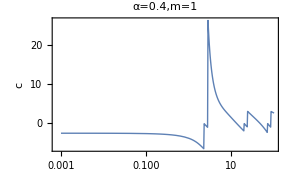

```mathematica
ListLogLinearPlot[c1a,ImageSize->290,Frame->True,Joined->True,PlotRange->All,Axes->False,FrameTicks->{{Automatic,None},{Automatic,None}},FrameLabel->{{"c",None},{"a",None}},PlotStyle->Thick,PlotLabel->Style["α=0.4,m=1",15],RotateLabel->False,FrameTicksStyle->{{{Bold,11},{}},{{Bold,11},{}}}]
Export["C:\\Users\\ASUS\\OneDrive\\Documents\\Test_6\\Plot_c1_veus_a_Alpha=0.4&m=1.eps",%];
```

```mathematica
c1a=({{100., 2.60965043279325594021985583854169100161542611292904814582706473279106986621699`50.}, {97.72372209558107, 2.66999494714975548174622060273565371761159914153402449110971162101373285405968`50.}, {95.49925860214358, 2.72934178430496060793901209362890666678034979421288690365593087499936612092257`50.}, {93.3254300796991, 2.78773508982820128546321277783665411462529909993900484799873117834831921456953`50.}, {91.20108393559097, 2.8452192125145935484956334211193525256086538085658891131756410486818305216555`50.}, {89.12509381337455, 2.901838776081642056084946036561861529299386866558662571731238686864913988986`50.}, {87.09635899560806, 2.95763875522638046507598681227359674893023299771982416467318983309358659240895`50.}, {85.11380382023764, 3.01266455653946494450465159381491707810851883099466065771581142855454354754839`50.}, {83.17637711026708, -0.95480766217677853768819318247551564127206775865907237126500129294429112416675`50.}, {81.2830516164099, -0.82120729919314755518300330550118815153837141178779431576253092611087602125174`50.}, {79.43282347242814, -0.69036423320862466690428504989540670067071909117982446311709811978569215146147`50.}, {77.62471166286916, -0.56219362655588128729888808265968691557645430160943413213221168886337456448162`50.}, {75.85775750291836, -0.43661144947375860048133233703993028029799437668517097928644231795620031163964`50.}, {74.13102413009177, -0.31353442552639013141124735284392954781651487397755244634276848857570036382804`50.}, {72.44359600749898, -0.19287997956226222984188467535204836167394645921670029143107257416377615383454`50.}, {70.79457843841381, -0.07456618859686073991221988421784772071980337807316968308144770420611420152064`50.}, {69.18309709189366, -2.29629853292900355100523510403031910305036563315993895109013787197498484361946`50.}, {67.60829753919819, -2.13930216008589849654927007831020379529600724132665661117321974611407294494661`50.}, {66.06934480075961, -1.98559669774154590251497698443128100512200079597813527891384894017966568021137`50.}, {64.56542290346556, -1.83507749310160207386627371825628754619665192125958813126210686079615634685862`50.}, {63.09573444801933, -1.68764058868269424515153730120919180101409590249677629702091978375726795379552`50.}, {61.65950018614822, -1.54318263590903472816134425583014888269023622839843809997483714343086608862658`50.}, {60.25595860743578, -1.40160081022218629026108945246278317863318917654533231156800742285593335243857`50.}, {58.8843655355589, -1.26279272816703368458866921846625274726821352029882536982321024749124337816777`50.}, {57.543993733715695, -1.12665636701602019795836844779024272720680330734413492586323674782938969354197`50.}, {56.23413251903491, -0.99308998760874384048591423379548359662294387817385654249535410862351499930963`50.}, {54.954087385762456, -0.86199206121714505579589626904635224491357803344728741667068499908691369891873`50.}, {53.70317963702527, -0.73326120139976153078364973225689027458429336547855991958069384243705094235547`50.}, {52.48074602497726, -0.60679610198406902510370741765655111521482467651366249690627915941670332445008`50.}, {51.28613839913648, -0.48249548251543508681216110289824428036808967590335334696331387152442680897015`50.}, {50.11872336272722, -0.36025804273648934228369000720704207196831703186034192881037089689630547041266`50.}, {48.97788193684461, -0.23998242791214254021614493694869452156126499176026051677601123036585156828889`50.}, {47.86300923226383, -0.12156720709309538214215606899415433872491121292114829246023694402915694939947`50.}, {46.77351412871981, -0.00491086671205489535760313479784144874429330229759227802111267896759106656034`50.}, {45.708818961487495, 0.11008817777220802406849079319802885014368041397342701776760099852325457081757`50.}, {44.6683592150963, 0.22353154913582492360196756313907266500469996039223234725012489896818550796088`50.}, {43.65158322401661, 0.33552085117811133556771158732461762533434421644213391824912010102229494070763`50.}, {42.65795188015925, 0.44615758335010948423352928063353176442605239834746330066008309640852358057158`50.}, {41.68693834703355, 0.55554302327569787461854107625403631489991330822854286788069429129419562522392`50.}, {40.73802778041126, 0.66377807304498000685219813271078170045528433985448438841911227352863706000911`50.}, {39.810717055349734, 0.77096306512643163109824395315782989544377419947254399780306793807585800567473`50.}, {38.904514499428046, 0.87719752392031560102846962101320430471361651910194066463764788810062088791025`50.}, {38.018939632056124, 0.98257987944686382786688467920729584012182553390192469146601501240319156183611`50.}, {37.15352290971726, 1.08720713053821731308846586514435608875076593592600394675478374678327579859068`50.}, {36.30780547701014, 1.19117445631014735623425284619086595762987268060600987460650293174149900708632`50.}, {35.48133892335755, 1.29457477677571450825663570119209243776258840782138139493263360260803042717834`50.}, {34.673685045253166, 1.39749826638391731864482182826164387979396212207606916797972218684941626477918`50.}, {33.884415613920254, 1.5000318281754615418850384779538700320308472165072583789699859286376255171395`50.}, {33.11311214825911, 1.60225854126999013065959381801901009757202446494065252907466758182301840504615`50.}, {32.359365692962825, 1.70425710059853001497622056289667449846147363212791529863571366741341049043741`50.}, {31.622776601683793, 1.80610127512661407565905782503625687057571895670996873572397294950627990018898`50.}, {30.902954325135905, 1.90785941906702102966408836118050490011279157140811830008933224865384763801743`50.}, {30.19951720402016, 2.00959407931686867450540396938055052940922231684020646601967103272568744785049`50.}, {29.512092266663856, 2.11136175084701221981787734425410857662665097427768799760300645231227914390723`50.}, {28.84031503126606, 2.21321283897988650240190931504632224394535457324590002137964985678309801925257`50.}, {28.183829312644534, 2.31519189207383045483493413180936406818555709377039426752551310082524660575006`50.}, {27.542287033381662, 2.41733816854590304513679385213536319388921729834506215632204934810207334359983`50.}, {26.915348039269155, 2.51968659687036882464214618923562573089980538361312248494756530290306523326632`50.}, {26.302679918953814, 2.62226917495802115513181253040399972061080189558656186467321063808981214871905`50.}, {25.703957827688647, 2.72511683562759478865740815194729354763378676667541593430126663851931219931274`50.}, {25.118864315095795, 2.82826177830393883741166274885015025049723594963678386232345453149423882604468`50.}, {24.547089156850312, 2.93174023559010578384117481177599482210832895711336174463688256929161396559066`50.}, {23.9883291901949, 3.03559561036848002358656713821349142815998391576519119140298008340842449808645`50.}, {23.442288153199225, -0.88654696233916269187957936992461327463387195439391211335780765240174712253398`50.}, {22.908676527677724, -0.76913827123034000932122467020235490053892108862773724131562463963128024234224`50.}, {22.3872113856834, -0.65221830085065374271735549882578197866678236009890980127316991809102610908459`50.}, {21.87761623949552, -0.53569209001287126925561210555315483361482620035421205636087316904881550912477`50.}, {21.379620895022324, -0.41947124448805059304667963715473888441919809153876398491500787594124692672171`50.}, {20.892961308540386, -0.30347425767299460175330239053437253460288007209438999977953003764901048579028`50.}, {20.417379446695296, -0.18762678055752203543082856640467070974409578690295139933712684085740895377802`50.}, {19.952623149688787, -0.07186184399150303409031792511996172834187739203638774775981714560896224149144`50.}, {19.498445997580454, -1.91386647903503116655514096471120291575524083523117666179552844944315694887418`50.}, {19.054607179632473, -1.80351184499761478404585027499719194301938673345629283164794875611943227789248`50.}, {18.620871366628677, -1.69312095370927353248963425757068178046466747879124788830330974916037972842375`50.}, {18.197008586099834, -1.58260579875413841289723878623800598694090344749751631477837079441889563489554`50.}, {17.78279410038923, -1.47189088667909193902679621912839883933451778834550394716278781764013337263594`50.}, {17.378008287493753, -1.36091329198602115244734295568752112290820752812404331029925139528550775567668`50.}, {16.982436524617444, -1.24962238049697982585092085925003962201912960065457587766191024655546000914351`50.}, {16.595869074375607, -1.13797920332046583265319372441253339022172806909558043911079179181117752990602`50.}, {16.218100973589298, -1.02595558808879651353461561875579078758801627380248966858019801037405232897054`50.}, {15.848931924611133, -0.91353297869936084252273644779052119702100753784179788760855609346409423947134`50.}, {15.488166189124811, -0.8007010966575762167529717316938331350684165542566313351271578770279990901504`50.}, {15.13561248436208, -0.68745651349243769301367024127102922648191452026363816539446970456384826234598`50.}, {14.791083881682072, -0.57380123226073181941231382552359718829393386840820160922078070102069354519157`50.}, {14.45439770745928, -0.45974137537277168230609447618917329236865043640133683963960525287236585606672`50.}, {14.12537544622754, -0.34528606543433978948165474776033079251646995544434306514419089940051740575889`50.}, {13.803842646028853, -0.23044656620857818796199723010431625880300998687743980824676248360793701678655`50.}, {13.489628825916533, -0.11523572386224372604557331101204908918589353561400545796643359896962646696032`50.}, {13.182567385564074, 0.00033228317584390682829089275026933417594361277772515040124788995377918973031`50.}, {12.882495516931336, 0.1162419112675015908382883187879707874099293632925696106160844294045008565896`50.}, {12.589254117941675, 0.23247599389481880956735464845908735070084797510843851957957013983373913398013`50.}, {12.30268770812381, 0.34901534653769832334222008947012269488501826715939250461898147978917839444253`50.}, {12.02264434617413, 0.46583834365937968389244745953429524395563464836248875144003008499011770738395`50.}, {11.748975549395292, 0.58292059072965747534909979884043045968924922440719505288370590875642282466109`50.}, {11.481536214968829, 0.70023481686255050768278863562868314503666140661077681059687714820724454850174`50.}, {11.220184543019629, 0.81775110445625374545595802325200450656718846163013277229230271242585970750953`50.}, {10.964781961431852, 0.93543755101578333132115821200180391209537695068787992884903858250823638515129`50.}, {10.715193052376065, 1.05326142613623051562336192214300105747337228298122018008549906873013766061858`50.}, {10.471285480508996, 1.17119084585064663538467172662860357204725933613780875084939260877217003327044`50.}, {10.232929922807541, 1.28919694104174382529006630988666541429320413164002429431216207618774072398675`50.}, {10., 1.40725645135240699385249224679652557113301751034369155548004041287373150798782`50.}, {9.772372209558107, 1.52535463650360350151918030250460020538526104120342749697109199735181959337052`50.}, {9.549925860214358, 1.64348836829151243670119891685206441279586546811206940694689069315728194120673`50.}, {9.33254300796991, 1.76166925265001631299486496011553984190836603776977386184438802100826193901976`50.}, {9.120108393559097, 1.87992663381978376540181916831955763517106935895886882620360668959921105949711`50.}, {8.912509381337454, 1.9983103511945029552974780911663277291103082818926334160571771116430532206032`50.}, {8.709635899560805, 2.11689315083471025834449048928110334486618802057271905489632019882328866679071`50.}, {8.511380382023763, 2.23577269328348321283747502629901301230311400663702011786699964307502130264569`50.}, {8.31763771102671, 2.35507314179125167380490538048936568938133653955502644374823808567442769987721`50.}, {8.128305161640993, 2.47494635525117640112904000798994301771122478635383036764529051868941069595632`50.}, {7.943282347242816, 2.59557274406619168989232643024963250565414858752413446490366467121146229699618`50.}, {7.762471166286917, 2.71716187240312271683411874537524387499044819514624983122033217071047131963662`50.}, {7.5857757502918375, 2.83995290609140131689712551721156626345586781480286327627766922209926344347717`50.}, {7.413102413009175, 2.96421501246752764021266905388604448816487471655248811784380285769153965537864`50.}, {7.244359600749901, 3.09024781840924612519393345539989597515507520616132472590207426078950687495148`50.}, {7.079457843841379, 3.21838202780298686337188648679299227603741769373685013091462954301586360789899`50.}, {6.918309709189364, 3.34898029197701219534537346439268459049867696874145677410549085964588607718139`50.}, {6.760829753919817, 3.48243841821717911394445606855373802904112457187226387409745240695530057619059`50.}, {6.606934480075961, 3.61918699397756839124054210597082905235178896050047353199041681712438911113835`50.}, {6.456542290346556, 3.75969349898207910203960802213833145311994647578725366445622907313700581777935`50.}, {6.309573444801933, 3.90446497486355545174206190748526914452492993959298296236716093466837703803837`50.}, {6.165950018614822, 4.05405132276802589588089061844742476850245183512316809542789098622157309221385`50.}, {6.025595860743578, 4.20904930371558856198455445078926128706772146295478122400388682986491711784757`50.}, {5.88843655355589, 4.37010732459857658462614774048083199412355035822925595931330223733521629387556`50.}, {5.7543993733715695, 4.53793110463037918179662140314205776542775727534186901397772603962546402259367`50.}, {5.623413251903491, 4.7132903330004296284334055572756351575313500916911601876931466299532933079081`50.}, {5.495408738576246, 4.89702644871006597796180907575713389087618038363711376520574029435408520445405`50.}, {5.370317963702527, 5.09006169847328332136090570574981472875668607172478651836266480950497951360432`50.}, {5.248074602497725, 5.29340965876053585989109669693253315329711116932735571868181843121269318448807`50.}, {5.1286138399136485, 5.50818744435376085563614765456340501718978211190848725859067077713934900450704`50.}, {5.011872336272722, 5.73562986923186406825948746600209725388387362011453736211594028636891040247635`50.}, {4.897788193684462, 5.97710587758108069648654739471403761343234731819267612773959679613249998198539`50.}, {4.786300923226383, 6.23413762494229161971003240173723514926425434834831360822025601729386611842806`50.}, {4.677351412871981, 6.50842266411123843166798515348450845599593547121068328257898252489661186188933`50.}, {4.57088189614875, 6.80185978006227648947118753340149674445570250200252805958563495024763205710755`50.}, {4.46683592150963, 7.11657912617562453596999449223905975049176817745075189826955073135595383884636`50.}, {4.36515832240166, 7.45497744451386021497177809173612932589486333092158183845026627636535857218322`50.}, {4.265795188015927, 7.8197593109196392104051347827410397443857561256176813402574299840812308428091`50.}, {4.168693834703354, 8.21398553766634867616026974600462155091215525963118916677488701825807252027002`50.}, {4.073802778041127, 8.64113010028431374914083068758799606211095222609379703941496566207485713894467`50.}, {3.9810717055349722, 9.10514724109214731039426176376988922723151316778713841894843415683727825491693`50.}, {3.890451449942806, 9.61055075268474922932115285920504549018563710974473405998994519379476168420874`50.}, {3.801893963205613, 10.16250787650476908288501762488193840259485479226723462436340010836905229877576`50.}, {3.715352290971726, 10.76695078564703870919209487874434903732476590715188798628188840219105808698279`50.}, {3.630780547701014, 11.43070928435772999018309565446603002746250534970094759385546462896990490132836`50.}, {3.548133892335755, 12.16166918458532242444965950356441846978045895926521983191649830132225432623066`50.}, {3.4673685045253166, 12.96896185854151387502003444255595306312553810928327381250025500439526698859208`50.}, {3.3884415613920256, 13.86319177606457991915257804960912081974079178601603647888973708527560218842221`50.}, {3.311311214825911, 14.85671049631161521884478988090017326739197266105399757018084167002559903869197`50.}, {3.2359365692962827, 15.96394770001357996455867289385948907253777227118437395428747413841365668083187`50.}, {3.1622776601683795, 17.20181255993369440305447190165026151531948970485885768693089407840409255304095`50.}, {3.0902954325135905, 18.59018223652116735905234234673351032339555469173954837177445909795969063202515`50.}, {3.019951720402016, 20.15249879517024608671522185117188975593035804953593199520667098563461073182366`50.}, {2.9512092266663856, 21.91650169112343377290083598260147564666987773985213888160209599192370876191217`50.}, {2.8840315031266055, 23.91513058191757307579874376309166793524911326364108237646922257329882045304263`50.}, {2.8183829312644537, 26.18764316877217350061738587230862628880335282448924940575610541541756684416103`50.}, {2.7542287033381663, -0.9954435870385341550173055205539907333940272472716815796019325213210466512644`50.}, {2.691534803926915, -0.88420006719175213255951734687129044948690980396410977855791348510574767963109`50.}, {2.630267991895382, -0.7729480027318453642154720570599222356432453107848730895641916827065191835726`50.}, {2.570395782768864, -0.66157218262564238532667221595417117332837260341647199408656457574958461160107`50.}, {2.51188643150958, -0.54994192896661344948240146212861808611738174661835061835462295088146156719544`50.}, {2.4547089156850306, -0.43791244901953511803276368207322390888965172954074158438395873356820918715871`50.}, {2.3988329190194904, -0.32532601739269807548378934595664891503665026375945041582764476535773102758521`50.}, {2.344228815319922, -0.21201297413446255264177402082631563245170592159122790238101350570104976763452`50.}, {2.290867652767773, -0.09779253324847074748918171510638404586361161415503246803752161473843883155317`50.}, {2.2387211385683394, -6.45137439299652608363764586943681827122296251146047642702821155998499264336235`50.}, {2.1877616239495525, -6.3417089838882614269086772331203471923960041582698045829859922921357452810043`50.}, {2.1379620895022318, -6.2322640008908446441224042155091792690832381674464035500320390201724578113092`50.}, {2.089296130854039, -6.12346368320970771870940242486280991869693974716318471878661774990353145495244`50.}, {2.041737944669529, -6.01569428899784457600008632646626733810853988916865757540808592894838252332646`50.}, {1.9952623149688793, -5.90930064593693041864867912090263460976206403685272884103195040385091272763937`50.}, {1.9498445997580456, -5.80458444610764678503027825589347641511124620571519980627132543792969255782925`50.}, {1.9054607179632472, -5.70180406233922125224996049536461272494214649952463820320091314769904498623483`50.}, {1.8620871366628675, -5.60117562019750058764978539501487442781221187679783654872842598325787406593654`50.}, {1.8197008586099834, -5.50287504589198249234598900214432420380595370306801230772679111194021583426199`50.}, {1.7782794100389228, -5.40704081953718484923762125176857262076738319238805962839153157328680930235581`50.}, {1.7378008287493754, -5.31377718847334860755367785996829126079390106597500086957767693205570174800853`50.}, {1.6982436524617444, -5.22315763015775737653488279137437470216941962468908551039145540179207262641907`50.}, {1.6595869074375604, -5.13522839294857732131356860175292442065182413653735071871315160048687251261184`50.}, {1.6218100973589298, -5.05001198173930053682898738006378843405977491514566211445438747519025578318967`50.}, {1.5848931924611134, -4.9675104910496124427989046898278413075171277059115966137305675366158643051003`50.}, {1.5488166189124812, -4.8877087192169024185352234251293497474734472826955214569534463501166960895447`50.}, {1.513561248436208, -4.81057702307578580618658274654536296178457371266584134480146192685276344386641`50.}, {1.4791083881682072, -4.73607389294131010941845958162283015299358023485994713208000016671250376900098`50.}, {1.4454397707459277, -4.66414824322694146199179904133397066263013392964857348865743972304167908482747`50.}, {1.4125375446227544, -4.59474142526412863246884471856870696410103079665786249890870737945499491303283`50.}, {1.3803842646028848, -4.52778897656634572822574925774451862533894901951148897447191919384985627015047`50.}, {1.3489628825916535, -4.46322212561304017672912285773802219513973287314713013693320360841797639840359`50.}, {1.318256738556407, -4.40096907387205076154381078663132086377801970518329592554451966108193733352552`50.}, {1.2882495516931338, -4.3409560777981510027248766229296984174745780690221476781057721473711076834291`50.}, {1.258925411794167, -4.28310835340854470441195238257716629190428937738724724457738413676744549579913`50.}, {1.2302687708123814, -4.22735082511624890904654717806842457499818068965758197894827041825965858783114`50.}, {1.2022644346174127, -4.1736087390882914345255760623376561284113536182279610247198338088813651614697`50.}, {1.1748975549395295, -4.12180815970315117498366912892006391396876503420864698531265990188114897502459`50.}, {1.1481536214968826, -4.07187636586788665062321579780963599026483767113980046316006223723730085785618`50.}, {1.1220184543019633, -4.02374216212970059986856415495787501085962482718394639687600451503551335697634`50.}, {1.096478196143185, -3.97733611775240317707289239496546304502232969940821829615512171698451816245295`50.}, {1.0715193052376064, -3.93259074527166724969431755422523747636733048291242802725540445980060887403889`50.}, {1.0471285480508996, -3.88944062852006646799768258437506375776716604100713187890316071481888782887427`50.}, {1.023292992280754, -3.84782250873551041708569200317347045287742993116741410713214991695676556024685`50.}, {1., -3.80767533613686464356434587747452866947429985487752815773523636914557822788069`50.}, {0.7943282347242815, -3.47524570032026146753895219883754062597219635786627913463723841484642839488995`50.}, {0.6309573444801932, -3.23823245684915386080141178947573930073751587893960717858911519524633401464265`50.}, {0.5011872336272722, -3.06580842987705982637821411086719555447994462375694705881162340223108516815012`50.}, {0.3981071705534972, -2.93815326780839882916138078902172973429670805070450812798547459892205371317904`50.}, {0.31622776601683794, -2.84227113090231993246808139898036560793437650059713448637659781631403161536588`50.}, {0.25118864315095796, -2.76941501234095396385532216290841614599945344212038634882436377517753949767998`50.}, {0.19952623149688792, -2.71354264469253544034846625746443274259103271845049644343598723388946867699029`50.}, {0.15848931924611134, -2.67038065626488850201295794075262238059939938012727926288887432512274009675078`50.}, {0.12589254117941673, -2.63684414021089397644043162224444668884871916759507353240572508481706399677069`50.}, {0.1, -2.61066698038625401588694518296258825411333476971839461799041047251827634527769`50.}, {0.039810717055349734, -2.55135498697038537389127897688283694912941564461377470395938004337434339150748`50.}, {0.015848931924611134, -2.52832678846949471213412088492883375792973811603501042160015655487280612158475`50.}, {0.00630957344480193, -2.51924977217140204168174565012505913649852895919070265588293235557158059006877`50.}, {0.0025118864315095794, -2.51565039737409956871598754746527163378410810762510035528191148013774823978378`50.}, {0.001, -2.51421971144978607052611892687434485426659617955906205076372357023499005523739`50.}})
```

{{100.,2.609650432793255940219855838541691001615426112929},{97.7237,2.669994947149755481746220602735653717611599141534},{95.4993,2.7293417843049606079390120936289066667803497942129},{93.3254,2.787735089828201285463212777836654114625299099939},{91.2011,2.8452192125145935484956334211193525256086538085659},{89.1251,2.9018387760816420560849460365618615292993868665587},{87.0964,2.9576387552263804650759868122735967489302329977198},{85.1138,3.0126645565394649445046515938149170781085188309947},{83.1764,-0.95480766217677853768819318247551564127206775865907},{81.2831,-0.82120729919314755518300330550118815153837141178779},{79.4328,-0.69036423320862466690428504989540670067071909117982},{77.6247,-0.56219362655588128729888808265968691557645430160943},{75.8578,-0.43661144947375860048133233703993028029799437668517},{74.131,-0.31353442552639013141124735284392954781651487397755},{72.4436,-0.1928799795622622298418846753520483616739464592167},{70.7946,-0.07456618859686073991221988421784772071980337807317},{69.1831,-2.2962985329290035510052351040303191030503656331599},{67.6083,-2.1393021600858984965492700783102037952960072413267},{66.0693,-1.9855966977415459025149769844312810051220007959781},{64.5654,-1.8350774931016020738662737182562875461966519212596},{63.0957,-1.6876405886826942451515373012091918010140959024968},{61.6595,-1.5431826359090347281613442558301488826902362283984},{60.256,-1.4016008102221862902610894524627831786331891765453},{58.8844,-1.2627927281670336845886692184662527472682135202988},{57.544,-1.1266563670160201979583684477902427272068033073441},{56.2341,-0.99308998760874384048591423379548359662294387817386},{54.9541,-0.86199206121714505579589626904635224491357803344729},{53.7032,-0.73326120139976153078364973225689027458429336547856},{52.4807,-0.60679610198406902510370741765655111521482467651366},{51.2861,-0.48249548251543508681216110289824428036808967590335},{50.1187,-0.36025804273648934228369000720704207196831703186034},{48.9779,-0.23998242791214254021614493694869452156126499176026},{47.863,-0.12156720709309538214215606899415433872491121292115},{46.7735,-0.0049108667120548953576031347978414487442933022975923},{45.7088,0.11008817777220802406849079319802885014368041397343},{44.6684,0.22353154913582492360196756313907266500469996039223},{43.6516,0.33552085117811133556771158732461762533434421644213},{42.658,0.44615758335010948423352928063353176442605239834746},{41.6869,0.55554302327569787461854107625403631489991330822854},{40.738,0.66377807304498000685219813271078170045528433985448},{39.8107,0.77096306512643163109824395315782989544377419947254},{38.9045,0.87719752392031560102846962101320430471361651910194},{38.0189,0.98257987944686382786688467920729584012182553390192},{37.1535,1.087207130538217313088465865144356088750765935926},{36.3078,1.191174456310147356234252846190865957629872680606},{35.4813,1.2945747767757145082566357011920924377625884078214},{34.6737,1.3974982663839173186448218282616438797939621220761},{33.8844,1.5000318281754615418850384779538700320308472165073},{33.1131,1.6022585412699901306595938180190100975720244649407},{32.3594,1.7042571005985300149762205628966744984614736321279},{31.6228,1.80610127512661407565905782503625687057571895671},{30.903,1.9078594190670210296640883611805049001127915714081},{30.1995,2.0095940793168686745054039693805505294092223168402},{29.5121,2.1113617508470122198178773442541085766266509742777},{28.8403,2.2132128389798865024019093150463222439453545732459},{28.1838,2.3151918920738304548349341318093640681855570937704},{27.5423,2.4173381685459030451367938521353631938892172983451},{26.9153,2.5196865968703688246421461892356257308998053836131},{26.3027,2.6222691749580211551318125304039997206108018955866},{25.704,2.7251168356275947886574081519472935476337867666754},{25.1189,2.8282617783039388374116627488501502504972359496368},{24.5471,2.9317402355901057838411748117759948221083289571134},{23.9883,3.0355956103684800235865671382134914281599839157652},{23.4423,-0.88654696233916269187957936992461327463387195439391},{22.9087,-0.76913827123034000932122467020235490053892108862774},{22.3872,-0.65221830085065374271735549882578197866678236009891},{21.8776,-0.53569209001287126925561210555315483361482620035421},{21.3796,-0.41947124448805059304667963715473888441919809153876},{20.893,-0.30347425767299460175330239053437253460288007209439},{20.4174,-0.18762678055752203543082856640467070974409578690295},{19.9526,-0.071861843991503034090317925119961728341877392036388},{19.4984,-1.9138664790350311665551409647112029157552408352312},{19.0546,-1.8035118449976147840458502749971919430193867334563},{18.6209,-1.6931209537092735324896342575706817804646674787912},{18.197,-1.5826057987541384128972387862380059869409034474975},{17.7828,-1.4718908866790919390267962191283988393345177883455},{17.378,-1.360913291986021152447342955687521122908207528124},{16.9824,-1.2496223804969798258509208592500396220191296006546},{16.5959,-1.1379792033204658326531937244125333902217280690956},{16.2181,-1.0259555880887965135346156187557907875880162738025},{15.8489,-0.9135329786993608425227364477905211970210075378418},{15.4882,-0.80070109665757621675297173169383313506841655425663},{15.1356,-0.68745651349243769301367024127102922648191452026364},{14.7911,-0.5738012322607318194123138255235971882939338684082},{14.4544,-0.45974137537277168230609447618917329236865043640134},{14.1254,-0.34528606543433978948165474776033079251646995544434},{13.8038,-0.23044656620857818796199723010431625880300998687744},{13.4896,-0.11523572386224372604557331101204908918589353561401},{13.1826,0.00033228317584390682829089275026933417594361277772515},{12.8825,0.11624191126750159083828831878797078740992936329257},{12.5893,0.23247599389481880956735464845908735070084797510844},{12.3027,0.34901534653769832334222008947012269488501826715939},{12.0226,0.46583834365937968389244745953429524395563464836249},{11.749,0.5829205907296574753490997988404304596892492244072},{11.4815,0.70023481686255050768278863562868314503666140661078},{11.2202,0.81775110445625374545595802325200450656718846163013},{10.9648,0.93543755101578333132115821200180391209537695068788},{10.7152,1.0532614261362305156233619221430010574733722829812},{10.4713,1.1711908458506466353846717266286035720472593361378},{10.2329,1.28919694104174382529006630988666541429320413164},{10.,1.4072564513524069938524922467965255711330175103437},{9.77237,1.5253546365036035015191803025046002053852610412034},{9.54993,1.6434883682915124367011989168520644127958654681121},{9.33254,1.7616692526500163129948649601155398419083660377698},{9.12011,1.8799266338197837654018191683195576351710693589589},{8.91251,1.9983103511945029552974780911663277291103082818926},{8.70964,2.1168931508347102583444904892811033448661880205727},{8.51138,2.235772693283483212837475026299013012303114006637},{8.31764,2.355073141791251673804905380489365689381336539555},{8.12831,2.4749463552511764011290400079899430177112247863538},{7.94328,2.5955727440661916898923264302496325056541485875241},{7.76247,2.7171618724031227168341187453752438749904481951462},{7.58578,2.8399529060914013168971255172115662634558678148029},{7.4131,2.9642150124675276402126690538860444881648747165525},{7.24436,3.0902478184092461251939334553998959751550752061613},{7.07946,3.2183820278029868633718864867929922760374176937369},{6.91831,3.3489802919770121953453734643926845904986769687415},{6.76083,3.4824384182171791139444560685537380290411245718723},{6.60693,3.6191869939775683912405421059708290523517889605005},{6.45654,3.7596934989820791020396080221383314531199464757873},{6.30957,3.904464974863555451742061907485269144524929939593},{6.16595,4.0540513227680258958808906184474247685024518351232},{6.0256,4.2090493037155885619845544507892612870677214629548},{5.88844,4.3701073245985765846261477404808319941235503582293},{5.7544,4.5379311046303791817966214031420577654277572753419},{5.62341,4.7132903330004296284334055572756351575313500916912},{5.49541,4.8970264487100659779618090757571338908761803836371},{5.37032,5.0900616984732833213609057057498147287566860717248},{5.24807,5.2934096587605358598910966969325331532971111693274},{5.12861,5.5081874443537608556361476545634050171897821119085},{5.01187,5.7356298692318640682594874660020972538838736201145},{4.89779,5.9771058775810806964865473947140376134323473181927},{4.7863,6.2341376249422916197100324017372351492642543483483},{4.67735,6.5084226641112384316679851534845084559959354712107},{4.57088,6.8018597800622764894711875334014967444557025020025},{4.46684,7.1165791261756245359699944922390597504917681774508},{4.36516,7.4549774445138602149717780917361293258948633309216},{4.2658,7.8197593109196392104051347827410397443857561256177},{4.16869,8.2139855376663486761602697460046215509121552596312},{4.0738,8.6411301002843137491408306875879960621109522260938},{3.98107,9.1051472410921473103942617637698892272315131677871},{3.89045,9.6105507526847492293211528592050454901856371097447},{3.80189,10.162507876504769082885017624881938402594854792267},{3.71535,10.766950785647038709192094878744349037324765907152},{3.63078,11.430709284357729990183095654466030027462505349701},{3.54813,12.161669184585322424449659503564418469780458959265},{3.46737,12.968961858541513875020034442555953063125538109283},{3.38844,13.863191776064579919152578049609120819740791786016},{3.31131,14.856710496311615218844789880900173267391972661054},{3.23594,15.963947700013579964558672893859489072537772271184},{3.16228,17.201812559933694403054471901650261515319489704859},{3.0903,18.59018223652116735905234234673351032339555469174},{3.01995,20.152498795170246086715221851171889755930358049536},{2.95121,21.916501691123433772900835982601475646669877739852},{2.88403,23.915130581917573075798743763091667935249113263641},{2.81838,26.187643168772173500617385872308626288803352824489},{2.75423,-0.99544358703853415501730552055399073339402724727168},{2.69153,-0.88420006719175213255951734687129044948690980396411},{2.63027,-0.77294800273184536421547205705992223564324531078487},{2.5704,-0.66157218262564238532667221595417117332837260341647},{2.51189,-0.54994192896661344948240146212861808611738174661835},{2.45471,-0.43791244901953511803276368207322390888965172954074},{2.39883,-0.32532601739269807548378934595664891503665026375945},{2.34423,-0.21201297413446255264177402082631563245170592159123},{2.29087,-0.097792533248470747489181715106384045863611614155032},{2.23872,-6.4513743929965260836376458694368182712229625114605},{2.18776,-6.3417089838882614269086772331203471923960041582698},{2.13796,-6.2322640008908446441224042155091792690832381674464},{2.0893,-6.1234636832097077187094024248628099186969397471632},{2.04174,-6.0156942889978445760000863264662673381085398891687},{1.99526,-5.9093006459369304186486791209026346097620640368527},{1.94984,-5.8045844461076467850302782558934764151112462057152},{1.90546,-5.7018040623392212522499604953646127249421464995246},{1.86209,-5.6011756201975005876497853950148744278122118767978},{1.8197,-5.502875045891982492345989002144324203805953703068},{1.77828,-5.4070408195371848492376212517685726207673831923881},{1.7378,-5.313777188473348607553677859968291260793901065975},{1.69824,-5.2231576301577573765348827913743747021694196246891},{1.65959,-5.1352283929485773213135686017529244206518241365374},{1.62181,-5.0500119817393005368289873800637884340597749151457},{1.58489,-4.9675104910496124427989046898278413075171277059116},{1.54882,-4.8877087192169024185352234251293497474734472826955},{1.51356,-4.8105770230757858061865827465453629617845737126658},{1.47911,-4.7360738929413101094184595816228301529935802348599},{1.44544,-4.6641482432269414619917990413339706626301339296486},{1.41254,-4.5947414252641286324688447185687069641010307966579},{1.38038,-4.5277889765663457282257492577445186253389490195115},{1.34896,-4.4632221256130401767291228577380221951397328731471},{1.31826,-4.4009690738720507615438107866313208637780197051833},{1.28825,-4.3409560777981510027248766229296984174745780690221},{1.25893,-4.2831083534085447044119523825771662919042893773872},{1.23027,-4.2273508251162489090465471780684245749981806896576},{1.20226,-4.173608739088291434525576062337656128411353618228},{1.1749,-4.1218081597031511749836691289200639139687650342086},{1.14815,-4.0718763658678866506232157978096359902648376711398},{1.12202,-4.0237421621297005998685641549578750108596248271839},{1.09648,-3.9773361177524031770728923949654630450223296994082},{1.07152,-3.9325907452716672496943175542252374763673304829124},{1.04713,-3.8894406285200664679976825843750637577671660410071},{1.02329,-3.8478225087355104170856920031734704528774299311674},{1.,-3.8076753361368646435643458774745286694742998548775},{0.794328,-3.4752457003202614675389521988375406259721963578663},{0.630957,-3.2382324568491538608014117894757393007375158789396},{0.501187,-3.0658084298770598263782141108671955544799446237569},{0.398107,-2.9381532678083988291613807890217297342967080507045},{0.316228,-2.8422711309023199324680813989803656079343765005971},{0.251189,-2.7694150123409539638553221629084161459994534421204},{0.199526,-2.7135426446925354403484662574644327425910327184505},{0.158489,-2.6703806562648885020129579407526223805993993801273},{0.125893,-2.6368441402108939764404316222444466888487191675951},{0.1,-2.6106669803862540158869451829625882541133347697184},{0.0398107,-2.5513549869703853738912789768828369491294156446138},{0.0158489,-2.528326788469494712134120884928833757929738116035},{0.00630957,-2.5192497721714020416817456501250591364985289591907},{0.00251189,-2.5156503973740995687159875474652716337841081076251},{0.001,-2.5142197114497860705261189268743448542665961795591}}